{{0,1},{0.1,1.22105},{0.2,1.48886},{0.3,1.81158},{0.4,2.19914},{0.5,2.66368},{0.6,3.22005},{0.7,3.88634},{0.8,4.68469},{0.9,5.64212},{1.,6.79164},{1.1,8.17356},{1.2,9.83712},{1.3,11.8425},{1.4,14.263},{1.5,17.1886},{1.6,20.7286},{1.7,25.0171},{1.8,30.2174},{1.9,36.5293},{2.,44.1966}}

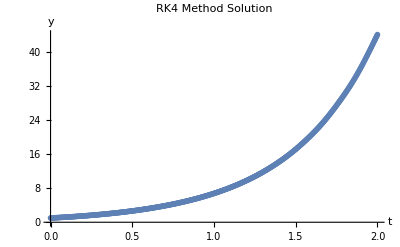

```mathematica
(*Define the differential equation*)
f[t_,y_]:=2y-t^2

(*Initial conditions*)
y0=1;
t0=0;
h=0.1;(*step size*)tEnd=2;

(*RK4 step function*)
rk4Step[f_,t_,y_,h_]:=Module[{k1,k2,k3,k4},k1=h f[t,y];
k2=h f[t+h/2,y+k1/2];
k3=h f[t+h/2,y+k2/2];
k4=h f[t+h,y+k3];
y+(k1+2 k2+2 k3+k4)/6]

(*RK4 solver*)
rk4Solve[f_,y0_,t0_,tEnd_,h_]:=Module[{steps,t,y,result},steps=Round[(tEnd-t0)/h];
result={{t0,y0}};
{t,y}={t0,y0};
Do[y=rk4Step[f,t,y,h];
t+=h;
AppendTo[result,{t,y}],{steps}];
result]

(*Solve the ODE*)
solution=rk4Solve[f,y0,t0,tEnd,h]

(*Plot the solution*)
ListLinePlot[solution,InterpolationOrder->6,PlotMarkers->Red,PlotStyle->Dashed,AxesLabel->{"t","y"},PlotLabel->"RK4 Method Solution"]
```

```mathematica
ClearAll[f,rk4]

f[x_,y_]:=x^2+y^2

rk4[x0_,y0_,h_]:=Module[{k1,k2,k3,k4},k1=h f[x0,y0];
k2=h f[x0+0.5 h,y0+0.5 k1];
k3=h f[x0+0.5 h,y0+0.5 k2];
k4=h f[x0+h,y0+k3];
y0+(k1+2 k2+2 k3+k4)/6]

(*Given initial conditions*)
x0=1;
y0=1.2;
h=0.05;

(*Calculate y(1.05)*)
y1=rk4[x0,y0,h];

Print["Approximate value of y(1.05) using RK4: ",y1]
```

Approximate value of y(1.05) using RK4: 1.33256